```mathematica
data = Import["/net/home/f09/bajennissen/research/DAY193_cloudy/sec_int_data/862nm.dat"]
```

{{1.46129,-0.23761},{1.36603,-0.167378},{1.32759,-0.185812},{1.2815,-0.175926},{1.23231,-0.186149},{1.21009,-0.164816},{1.18279,-0.294103},{1.15809,-0.679935},{1.13892,-1.10891},{1.12738,-1.44919},{1.09219,-1.03114},{1.09146,-0.603818},{1.09503,-0.202177},{1.10053,-0.141817},{1.1079,-0.14372},{1.12128,-0.141748},{1.13179,-0.136656},{1.14273,-0.143166},{1.16583,-0.154259},{1.1846,-0.1498},{1.20387,-0.0935747},{1.22314,-0.121456},{1.24682,-0.142324}}

-1.84075+1.25877 x

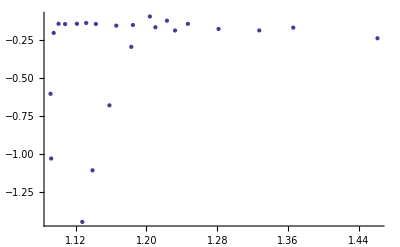

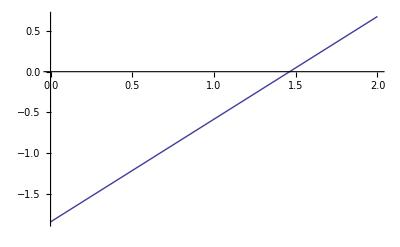

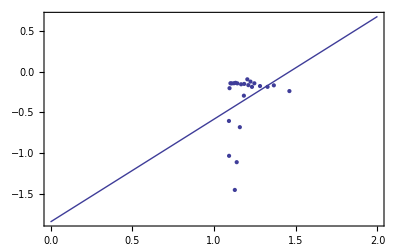

```mathematica
line = Fit[data,{1,x},x]
DataPlot=ListPlot[data]
FitPlot=Plot[line,{x,0,2}]
Show[DataPlot,FitPlot,PlotRange->All,Frame->True,AxesOrigin->{0,0}]
```